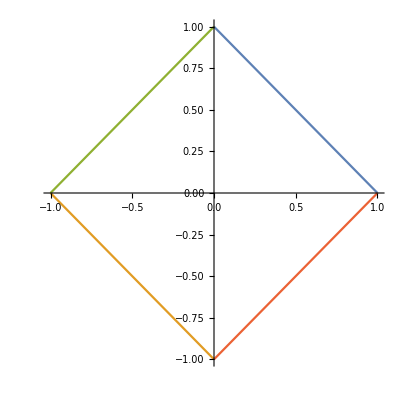

```mathematica
ParametricPlot[{{0.5-t,0.5+t},{-0.5-t,-0.5+t},{-0.5+t,0.5+t},{0.5+t,-0.5+t}},{t,-0.5,0.5}]
```

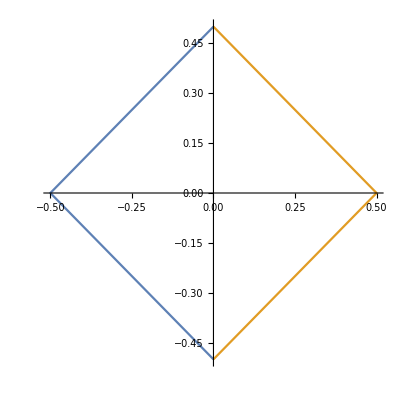

```mathematica
ParametricPlot[{{Abs[t]-0.5,t},{-Abs[t]+0.5,t}},{t,-0.5,0.5}]
```

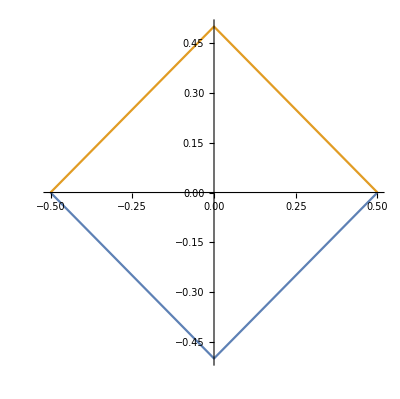

```mathematica
ParametricPlot[{{t,Abs[t]-0.5 },{t,-Abs[t]+0.5 }},{t,-0.5,0.5}]
```

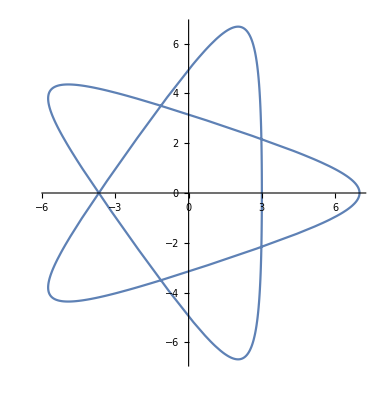

```mathematica
ParametricPlot[{2Cos[t]+5Cos[(2t)/3],2Sin[t]-5Sin[(2t)/3]},{t,0,6π}]
```

```mathematica
Manipulate[
ParametricPlot[{
{a Cos[t]+b Cos[(2t)/3],a Sin[t]-b Sin[(2t)/3]},
{a Cos[t],a Sin[t]},{b Cos[t],b Sin[t]}
},{t,0,n π}],
{a,1,5,1},{b,2,8},{n,1,6}]
```

```mathematica
Manipulate[
ParametricPlot[{Sin[θ],Sin[n θ+ϕ]},{θ,0,t},PlotRange->1.1],
{n,1,20},{ϕ,0,π/2},{t,0.01,10π}]
```

```mathematica
Manipulate[
ParametricPlot[{Sin[p θ],Sin[q θ+ϕ]},{θ,0,t},PlotRange->1.1],
{p,1,20},{q,1,20},{ϕ,0,π/(2p)},{t,0.01,2π}]
```

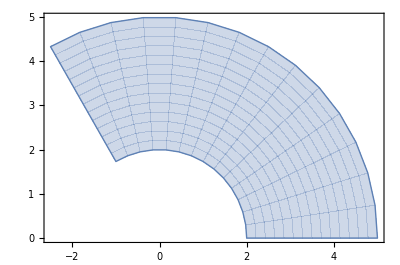

```mathematica
fx=ρ Cos[θ];
fy=ρ Sin[θ];
ParametricPlot[{fx,fy},{ρ,2,5},{θ,0,2 π/3}]
```